## Analyses

### TimeSeriesForecast

The Wolfram Language has inbuilt fuctions for generating TimeSeriesModels, and using those models to generate TimeSeriesForecasts.  These functions evaluate multiple time series processes, and return the process with the highest explanatory value.  As we will see, this automatic evaluation of multiple models does not guarantee that the model returned is the best possible model to describe the data.

#### TimeSeriesModelFit

```mathematica
loadTSModel=TimeSeriesModelFit[resampledNEISOLoad]
```

TimeSeriesModel[…]

```mathematica
loadTSModelforecast=TimeSeriesForecast[loadTSModel,{72}]
```

TemporalData[…]

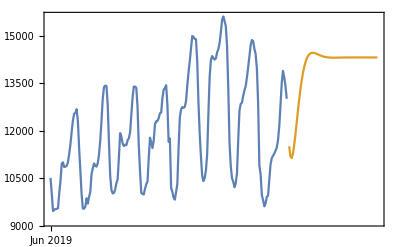

```mathematica
tsmodelDLP=DateListPlot[{
	TimeSeriesWindow[
	resampledNEISOLoad,
	{DateObject[{2019,6,1}],
	DateObject[{2019,6,8}]}],loadTSModelforecast}]
```

#### TimeSeriesForecast specifying SARIMA with Automatic Options

```mathematica
tsmodelSARIMA=TimeSeriesModelFit[resampledNEISOLoad,{"SARIMA",{Automatic,Automatic,Automatic}}]
```

TimeSeriesModel[…]

```mathematica
loadTSModelforecastSARIMA=TimeSeriesForecast[tsmodelSARIMA,{72}]
```

TemporalData[…]

```mathematica
tsmodelDLPSARIMA=DateListPlot[{
	TimeSeriesWindow[
	resampledNEISOLoad,
	{DateObject[{2019,6,1}],
	DateObject[{2019,6,8}]}],loadTSModelforecastSARIMA}]
```

-Graphics-

#### TimeSeriesForecast specifying SARIMA with Specified Options

```mathematica
tsmodelSARIMASpecified=TimeSeriesModelFit[resampledNEISOLoad,{"SARIMA",{{1,1,1},{1,1,1},24}}]
```

TimeSeriesModel[…]

```mathematica
loadTSModelforecastSARIMASpecified=TimeSeriesForecast[tsmodelSARIMASpecified,{72}]
```

TemporalData[…]

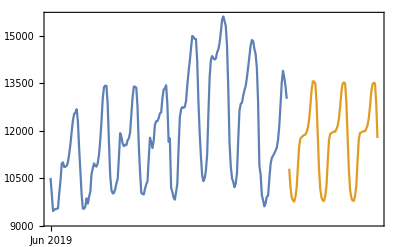

```mathematica
tsmodelDLPSARIMASpecified=DateListPlot[{
	TimeSeriesWindow[
	resampledNEISOLoad,
	{DateObject[{2019,6,1}],
	DateObject[{2019,6,8}]}],loadTSModelforecastSARIMASpecified}]
```